collimated output of the fiber

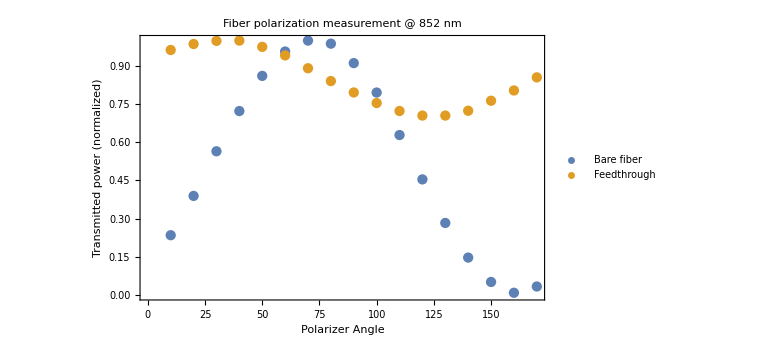

```mathematica
data = {.448,.743,1.078,1.380,1.644,1.827,1.909,1.886,1.74,1.519,1.2,.867,.54,.28,.097,.016,.063};
steps= Array[10#&,17];(*waveplate angle*)
dataBare = data/Max[data];
data = {0.859,0.88,0.891,0.892,0.87,0.84,0.795,0.75,0.71,0.673,.645,.629,.629,.646,.681,.717,.763};
dataFeedthrough = data/Max[data];
ListPlot[{Transpose@{steps,dataBare},Transpose@{steps,dataFeedthrough}},PlotRange->{0,1},Frame-> {True,True,False,False},Axes-> False,PlotLabel->"Fiber polarization measurement @ 852 nm",FrameLabel-> {"Polarizer Angle","Transmitted power (normalized)"},PlotLegends->{"Bare fiber","Feedthrough"}, LabelStyle->Directive[Black,FontSize-> 14],ImageSize->Large]
```

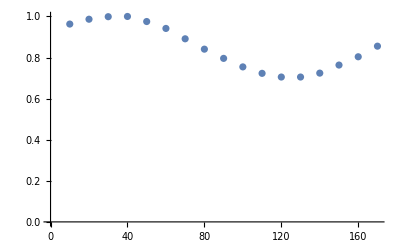

```mathematica
data = {0.859,0.88,0.891,0.892,0.87,0.84,0.795,0.75,0.71,0.673,.645,.629,.629,.646,.681,.717,.763};
steps= Array[10#&,17];(*waveplate angle*)
data = data/Max[data];
ListPlot[Transpose@{steps,data},PlotRange->{0,1}]
```